# Time-Correlated Guassian Jittering Dark SRF

## Toy Model

#### Parameters for the toy model

```mathematica
toyomega0=1;
toygamma=toyomega0/100;
toydelomega=toyomega0/10;
toytjit=3;
toyF=1;
toyomegaF=1;
x0=0;
dx0=0;
toytf=400;
```

#### Simluation

```mathematica
f[m_]:=E^(-m/3);(*correlation function. time scale tau=1s, with the time step 3s hence the denominator 3=1*3 *)
```

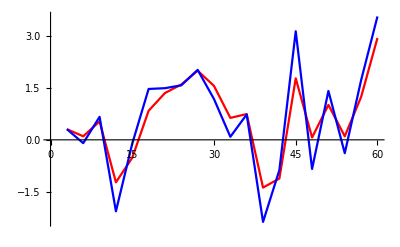

```mathematica
gtable=Table[{3 n,RandomVariate[NormalDistribution[0,1]]},{n,1,20}];(*generate an uncorrelated normal distribution g*)
rTable=Table[
{3 n,g[3 n-3]*gtable[[1,2]]+
Sqrt[1-f[1]^2] *Sum[f[3 n-3i]*gtable[[i,2]],{i,2,n}]},
{n,1,20}];(*using the trick to generate a time correlated normal distribution r*)
ListLinePlot[{rTable,gtable},PlotStyle->{Red,Blue}]
```

```mathematica
g[m_]:=E^(-m/30);(*tau=10s, time step = 3s*)
```

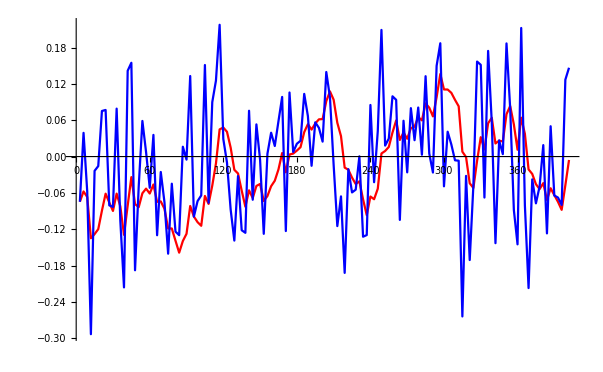

```mathematica
gtable=Table[{3 n,RandomVariate[NormalDistribution[0,toydelomega]]},{n,1,Ceiling[toytf/toytjit]*toytjit/3}];
rTable=Table[
{3 n,g[3 n-3]*gtable[[1,2]]+
Sqrt[1-g[1]^2] *Sum[g[3 n-3i]*gtable[[i,2]],{i,2,n}]},
{n,1,Ceiling[toytf/toytjit]*toytjit/3}];
ListLinePlot[{rTable,gtable},PlotStyle->{Red,Blue}]
```

#### Toy Model x(t)

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {(-1.15032×10^-9-1.53571×10^-9 ⅈ)[y] (1+Piecewise[{{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},{«2»},«124»},0])^2==Cos[y],True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0}.

NDSolve::dsvar: 0.00817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.856299 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.00817143]==0.999967,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0},-1.15032×10^-9-1.53571×10^-9 ⅈ,{0.00817143,0,400}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00817143 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0.856299 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.00817143]==0.999967,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0.]==0.},-1.15032×10^-9-1.53571×10^-9 ⅈ,{0.00817143,0.,400.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 8.17144 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0.870976 (-1.15032×10^-9-1.53571×10^-9 ⅈ)[8.17144]==-0.31215,True,(-1.15032×10^-9-1.53571×10^-9 ⅈ)[0]==0},-1.15032×10^-9-1.53571×10^-9 ⅈ,{8.17144,0,400}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

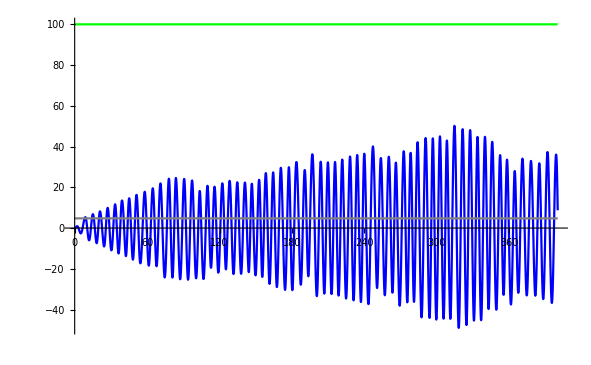

```mathematica
jitterdata=Table[{x,RandomVariate[NormalDistribution[0,toydelomega]]},{x,toytjit,Ceiling[toytf/toytjit]*toytjit,toytjit}];
jitter=Table[{jitterdata[[i,2]],y<jitterdata[[i,1]]},{i,1,Length[jitterdata]}];
solUC=NDSolve[{z''[y]+2 toygamma*z'[y]+(toyomega0+Piecewise[jitter])^2*z[y]==F*Cos[toyomegaF*y],z'[0]==dx0,z[0]==x0},z,{y,0,toytf}];
Rjitter=Table[{rTable[[i,2]],y<rTable[[i,1]]},{i,1,Length[rTable]}];
sol=NDSolve[{x''[y]+2 toygamma*x'[y]+(toyomega0+Piecewise[Rjitter])^2*x[y]==F*Cos[toyomegaF*y],x'[0]==dx0,x[0]==x0},x,{y,0,toytf}];
Plot[{x[y]/.sol,z[y]/.solUC,F/Sqrt[toygamma^2*toyomegaF^2],F/Sqrt[((toyomega0+toydelomega)^2-toyomegaF^2)^2+toygamma^2*toyomegaF^2]},{y,0,toytf},PlotStyle->{Red,Blue,Green,Gray}]
```

## Real Model

### Real Model Parameters

```mathematica
omega0=1.3*^9;
delomega0=4;
gamma=0.4;
F0=1;
m=1;
```

### Integrated Functions

```mathematica
xf[x0_,v0_,delomega_,t_,t0_]:=E^(-gamma*t/2)*(x0*Cos[(omega0+delomega)*t]+v0/(omega0+delomega)*Sin[(omega0+delomega)*t])+F0*E^(-I*omega0*(t+t0))/m/omega0/(2*delomega-I*gamma)*(1-E^(-gamma*t/2-I*delomega*t));
vf[x0_,v0_,delomega_,t_,t0_]:=E^(-gamma*t/2)*(-(omega0+delomega)*x0*Sin[(omega0+delomega)*t]+v0*Cos[(omega0+delomega)*t])-I*F0*E^(-I*omega0*(t+t0))/m/(2*delomega-I*gamma)*(1-E^(-gamma*t/2-I*delomega*t));
yf[x0_,v0_,delomega_,t_,t0_]:=xf[x0,v0,delomega,t,t0]+I*vf[x0,v0,delomega,t,t0]/omega0;
```

### δω Table

```mathematica
num=100000;(*total simulation points*)
g[m_]:=If[m<=100,E^(-m/10),0];(*correlation function g with correlation scale=10*time step=tau*)
```

```mathematica
gtable=Table[{n,RandomVariate[NormalDistribution[0,delomega0]]},{n,1,num}];(*uncorrelated δω*)
```

```mathematica
rtable=Table[0,{num}];  (*Initialize a list of zeros*)
rtable[[1]]=gtable[[1,2]]; 
For[n=2,n<=num,n++,rtable[[n]]=g[1]*rtable[[n-1]]+Sqrt[1-g[1]^2] gtable[[n,2]];];
rtable;(*correlated δω*)
```

```mathematica
(*Timing[
rtable=Table[
g[n-1]*gtable[[1,2]]+
Sqrt[1-g[1]^2] *Sum[g[n-i]*gtable[[i,2]],{i,2,n}],
{n,1,num}];
]*)
```

### Simulation for x(t)

```mathematica
tmin=0.0005;
tmax=0.01;
tstep=0.0005;
```

#### Time Correlated

```mathematica
mxstable={};
For[
t=tmin,t<=tmax,t+=tstep,(*t = simluation step, generally one order smaller than tau. tau=10*t *)
num=150000;
delomegas=rtable;
xs={0};
vs={0};
Do[
x=xs[[-1]];
v=vs[[-1]];
delomega=delomegas[[Length[xs]]];
t0=t*(Length[xs]-1);
AppendTo[xs,xf[x,v,delomega,t,t0]];
AppendTo[vs,vf[x,v,delomega,t,t0]];,num];
mxs=Mean[Table[Abs[xs[[i]]]^2,{i,50000,Length[xs]}]];
mxstable=Append[mxstable,mxs]
];
mxstable
```

```mathematica
mxstablefinal=Table[{i*5,mxstable[[i]]},{i,1,Length[mxstable]}]
```

```mathematica
{{5,2.874924684819396*^-18},{10,2.279880973708357*^-18},{15,1.744193150771779*^-18},{20,1.3752159221872344*^-18},{25,1.1562069926611414*^-18},{30,1.031929392709205*^-18},{35,9.53430217516971*^-19},{40,8.919554482582994*^-19},{45,8.328161636986378*^-19},{50,7.70969216708858*^-19},{55,7.082075243136309*^-19},{60,6.490214811926072*^-19},{65,5.966985914585215*^-19},{70,5.521500198067497*^-19},{75,5.150236186385221*^-19},{80,4.84956527835902*^-19},{85,4.616915790777861*^-19},{90,4.44525949830376*^-19},{95,4.320407907149715*^-19},{100,4.224376624593228*^-19}};
```

```mathematica
tc=0.001;(*A single run *)
numc=100000;
delomegas=rtable;
xs={0};
vs={0};
Do[
xc=xsc[[-1]];
vc=vsc[[-1]];
delomega=delomegas[[Length[xsc]]];
tc0=tc*(Length[xsc]-1);
AppendTo[xsc,xf[xc,vc,delomega,tc,tc0]];
AppendTo[vsc,vf[xc,vc,delomega,tc,tc0]];,numc]
```

#### Uncorrelated

```mathematica
mxsdtable={};
For[
t=10*tmin,t<=10*tmax,t+=10*tstep,
num=60000;
delomegasd=gtable[[All,2]];
xsd={0};
vsd={0};
Do[
xd=xsd[[-1]];
vd=vsd[[-1]];
delomegad=delomegasd[[Length[xsd]]];
t0=t*(Length[xsd]-1);
AppendTo[xsd,xf[xd,vd,delomegad,t,t0]];
AppendTo[vsd,vf[xd,vd,delomegad,t,t0]];,num];
mxsd=Mean[Table[Abs[xsd[[i]]]^2,{i,20000,Length[xsd]}]];
mxsdtable=Append[mxsdtable,mxsd]
]
mxsdtable
```

{3.08961×10^-18,2.58665×10^-18,2.23989×10^-18,1.97763×10^-18,1.76782×10^-18,1.59934×10^-18,1.46449×10^-18,1.35539×10^-18,1.265×10^-18,1.18818×10^-18,1.12178×10^-18,1.06389×10^-18,1.01315×10^-18,9.68268×10^-19,9.28049×10^-19,8.91447×10^-19,8.57656×10^-19,8.26139×10^-19,7.96545×10^-19,7.68692×10^-19}

```mathematica
mxsdtablefinal=Table[{i*5,mxsdtable[[i]]},{i,1,Length[mxsdtable]}]
```

```mathematica
{{5,3.0896100036858954*^-18},{10,2.586651370727505*^-18},{15,2.239885757088284*^-18},{20,1.9776339689692462*^-18},{25,1.76782208664291*^-18},{30,1.5993397904003394*^-18},{35,1.4644905321436057*^-18},{40,1.3553898797387193*^-18},{45,1.2649972620980373*^-18},{50,1.188182144263426*^-18},{55,1.1217820332324289*^-18},{60,1.0638943933740265*^-18},{65,1.0131475128914859*^-18},{70,9.682683536574985*^-19},{75,9.280491639611846*^-19},{80,8.91446589192379*^-19},{85,8.57655537646999*^-19},{90,8.261389973876772*^-19},{95,7.965445582267562*^-19},{100,7.686923998035928*^-19}};
```

```mathematica
tuc=0.01;(*a single run*)
numuc=10000;
delomegasd=gtable[[All,2]];
xsduc={0};
vsduc={0};
Do[
xduc=xsduc[[-1]];
vduc=vsduc[[-1]];
delomegad=delomegasd[[Length[xsduc]]];
tuc0=tuc*(Length[xsduc]-1);
AppendTo[xsduc,xf[xduc,vduc,delomegad,tuc,tuc0]];
AppendTo[vsduc,vf[xduc,vduc,delomegad,tuc,tuc0]];,numuc]
```

#### Predictions

```mathematica
newprediction=Table[{1000*ti,1/(omega0^2 (gamma+4^2*ti)^2)},{ti,tmin*10,tmax*10,tstep*10}](*the prediction for the correlated case*)(*for the uncorrelated case*)
nojitterprediction=Table[{1000*ti,1/(omega0^2 (gamma)^2)},{ti,tmin*10,tmax*10,tstep*10}];(*the prediction for the correlated case*)(*for the uncorrelated case*)
```

{{5.,2.56821×10^-18},{10.,1.88685×10^-18},{15.,1.44462×10^-18},{20.,1.14143×10^-18},{25.,9.24556×10^-19},{30.,7.64096×10^-19},{35.,6.42053×10^-19},{40.,5.47075×10^-19},{45.,4.71712×10^-19},{50.,4.10914×10^-19},{55.,3.61155×10^-19},{60.,3.19916×10^-19},{65.,2.85357×10^-19},{70.,2.5611×10^-19},{75.,2.31139×10^-19},{80.,2.0965×10^-19},{85.,1.91024×10^-19},{90.,1.74774×10^-19},{95.,1.60513×10^-19},{100.,1.47929×10^-19}}

### Plots

#### Color functions

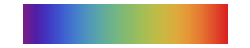

```mathematica
ColorData["Rainbow","Panel"]
```

```mathematica
RGBColor[0.858916696, 0.14327611938461532, 0.13425665599999997]RGBColor[0.8835435058461538, 0.32852485661538455, 0.16740855753846154]RGBColor[0.9013003181538461, 0.5627631778461536, 0.21272317907692306]RGBColor[0.574770582769231, 0.7389035593846154, 0.3872324910769229]RGBColor[0.5061138307692309, 0.7274670264615385, 0.44938891569230766]RGBColor[0.4291163667692309, 0.7013668276923077, 0.5414233427692307]RGBColor[0.2660948713846154, 0.4865096344615385, 0.8025456830769231]RGBColor[0.24431319138461538, 0.3564765895384616, 0.8144377698461539]RGBColor[0.28384562707692307, 0.16620879876923084, 0.7116890855384616]RGBColor[0.5956470381538463, 0.741960347076923, 0.3690455126153845]RGBColor[0.7693757526153846, 0.727185619076923, 0.2716108252307692]RGBColor[0.5886882196923078, 0.7409414178461539, 0.3751078387692307]
```

RGBColor[0.24431319138461538, 0.3564765895384616, 0.8144377698461539] RGBColor[0.2660948713846154, 0.4865096344615385, 0.8025456830769231] RGBColor[0.28384562707692307, 0.16620879876923084, 0.7116890855384616] RGBColor[0.4291163667692309, 0.7013668276923077, 0.5414233427692307] RGBColor[0.5061138307692309, 0.7274670264615385, 0.44938891569230766] RGBColor[0.574770582769231, 0.7389035593846154, 0.3872324910769229] RGBColor[0.5886882196923078, 0.7409414178461539, 0.3751078387692307] RGBColor[0.5956470381538463, 0.741960347076923, 0.3690455126153845] RGBColor[0.7693757526153846, 0.727185619076923, 0.2716108252307692] RGBColor[0.858916696, 0.14327611938461532, 0.13425665599999997] RGBColor[0.8835435058461538, 0.32852485661538455, 0.16740855753846154] RGBColor[0.9013003181538461, 0.5627631778461536, 0.21272317907692306]

```mathematica
Blue1=RGBColor[0.1,0.5,1]
Blue2=RGBColor[0.24,0.36,.81]
Blue3=RGBColor[0.28,0.17,.71]
```

RGBColor[0.1, 0.5, 1]

RGBColor[0.24, 0.36, 0.81]

RGBColor[0.28, 0.17, 0.71]

```mathematica
Green1=RGBColor[0.77,0.73,0.27]
Green2=RGBColor[0.51,0.73,0.45]
Green3=RGBColor[0.12,0.56,0.49]
```

RGBColor[0.77, 0.73, 0.27]

RGBColor[0.51, 0.73, 0.45]

RGBColor[0.12, 0.56, 0.49]

```mathematica
Red1=RGBColor[1,0.5,0]
Red2=RGBColor[0.90,0.38,0.10]
Red3=RGBColor[.86,.14,.13]
```

RGBColor[1, 0.5, 0]

RGBColor[0.9, 0.38, 0.1]

RGBColor[0.86, 0.14, 0.13]

#### Plot

```mathematica
leg1=LineLegend[{Black,Blue1,Green3,Red2},{Style["1/γ^2",FontFamily->"Times New Roman"],Style["Uncorrelated Gaussian Jittering",FontFamily->"Times New Roman"],Style["Time-correlated Gaussian Jittering",FontFamily->"Times New Roman"],Style["1/(γ + SuperscriptBox[δω, 2] τ)^2",FontFamily->"Times New Roman"]}]
```

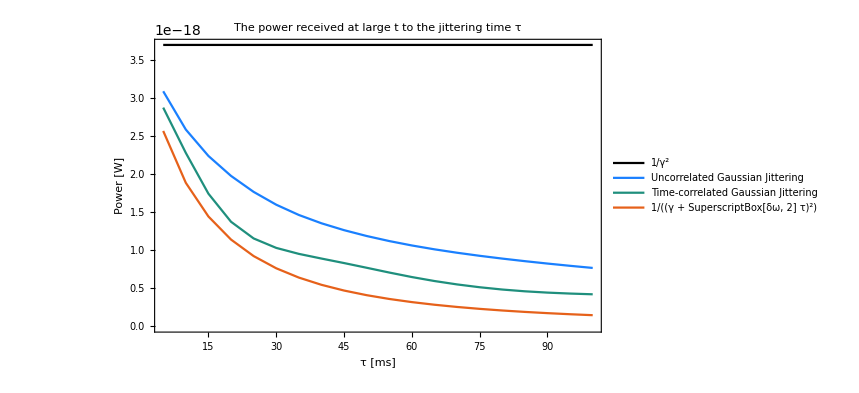

```mathematica
ListLinePlot[{newprediction,nojitterprediction,mxstablefinal,mxsdtablefinal},PlotStyle->{Red2,Black,Green3,Blue1},Frame->True,FrameLabel->(Style[#,14]&/@{"τ [ms]","Power [W]"}),PlotLegends->Placed[leg1,{0.8,0.55}],Frame->True,PlotRange->{{5,100},All},PlotLabel->"The power received at large t to the jittering time τ",Ticks->{{0,0},Automatic}]
```

```mathematica
Export["power of different tau.pdf",%181]
```

power of different tau.pdf

```mathematica
ListLinePlot[{Table[{tc*(i-1),Abs[F0]^2/m^2/(omega0^2 (gamma+4^2*10^(-2))^2)},{i,1,numc}],Table[{tc*(i-1),Abs[F0]^2/m^2/omega0^2/gamma^2},{i,1,numc}],Table[{tc*(i-1),Abs[xsc[[i]]]^2},{i,1,numc}],Table[{tuc*(i-1),Abs[xsduc[[i]]]^2},{i,1,numuc}]},PlotStyle->{Red2,Black,Green3,Blue1},Frame->True,FrameLabel->(Style[#,14]&/@{"time [s]","|x(t)|^2 "}),PlotLegends->Placed[leg1,Right],PlotRange->{{0,100},Automatic},Frame->True,PlotLabel->"The power calculated by different methods when τ=10ms"]
```

-Graphics-

```mathematica
Export["jittering of tau=10.pdf",%153]
```

jittering of tau=10.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["jittering of tau=10.pdf"]]]
```

## Others...

```mathematica
t=0.03;
num=50000;
delomega0=1;
delomegas=RandomVariate[NormalDistribution[0,delomega0],num];
xs={0};
vs={0};
Do[
x=xs[[-1]];
v=vs[[-1]];
delomega=delomegas[[Length[xs]]];
t0=t*(Length[xs]-1);
AppendTo[xs,xf[x,v,delomega,t,t0]];
AppendTo[vs,vf[x,v,delomega,t,t0]];,num]
```

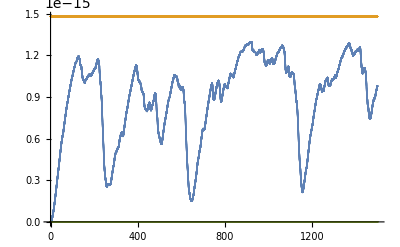

```mathematica
ListPlot[{Table[{t*(i-1),Abs[xs[[i]]+I*vs[[i]]/omega0]^2},{i,1,Length[xs]}],Table[{t*(i-1),4*Abs[F0]^2/m^2/omega0^2/gamma^2},{i,1,Length[xs]}],Table[{t*(i-1),Abs[F0]^2/m^2/omega0^2/gamma*t},{i,1,Length[xs]}]}]
```

```mathematica
n=6000;
x0=xs[[n]];
v0=vs[[n]];
delomega0=delomegas[[n]];
t0=t*(n-1);
y0=x0+I*v0/omega0//N
yf[x0,v0,delomega0,t,t0]
Abs[yf[x0,v0,delomega0,t,t0]]^2-Abs[y0]^2
(2/m/omega0*Im[Conjugate[F0]*y0*E^(I*omega0*t0)]-gamma*Abs[y0]^2)*t+Abs[F0]^2/m^2/omega0^2*t^2
{2/m/omega0*Im[Conjugate[F0]*y0*E^(I*omega0*t0)]*t,-gamma*Abs[y0]^2*t,Abs[F0]^2/m^2/omega0^2*t^2}
```

-2.82775×10^-8-1.0976×10^-8 ⅈ

5.71254×10^-9-2.97947×10^-8 ⅈ

2.66264×10^-19

2.68465×10^-19

{1.37204×10^-18,-1.10411×10^-18,5.32544×10^-22}

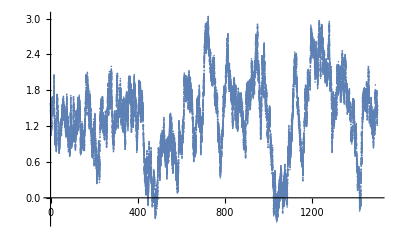

```mathematica
ListPlot[Table[{t*(i-1),Arg[Conjugate[F0]*(xs[[i]]+I*vs[[i]]/omega0)*E^(I*omega0*t*(i-1))]},{i,1,Length[xs]}]]
```

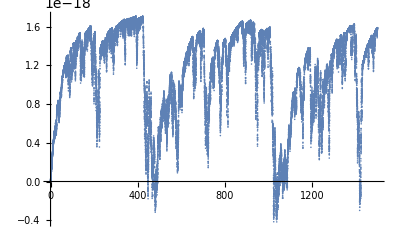

```mathematica
ListPlot[Table[{t*(i-1),2/m/omega0*Im[Conjugate[F0]*(xs[[i]]+I*vs[[i]]/omega0)*E^(I*omega0*t*(i-1))]*t},{i,1,Length[xs]}]]
```